```mathematica
Clear[R,ϵ];
```

```mathematica
S=(1/R)-(2p/((R-1)+√((R-1)^2+4*R*p)))
```

1/R

```mathematica
V=(ϵ*(R-1)+ϵ*√((R-1)^2+4*R*p))/(2*R)
```

((-1+R) ϵ+√((-1+R)^2) ϵ)/(2 R)

```mathematica
p=0
```

0

```mathematica
Solve[(1-R S+R V+ϵ)^2-4 (R V+ϵ-R S ϵ)==0,ϵ]
```

{{ϵ→0},{ϵ→(-4+4 √((-1+R)^2)+4 R)/(1+√((-1+R)^2)+√((-1+R)^2) R+R^2)}}

```mathematica
h[R_]:=(-4+4 √((-1+R)^2)+4 R)/(1+√((-1+R)^2)+√((-1+R)^2) R+R^2)
```

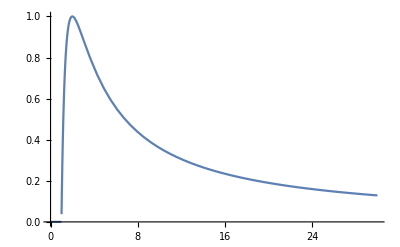

```mathematica
Plot[g[R],{R,0,30}]
```

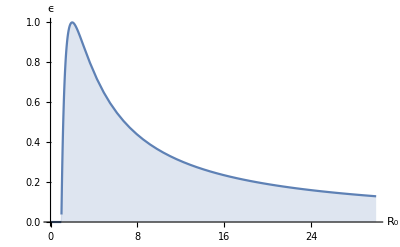

```mathematica
Plot[g[R],{R,0,30},Filling->Bottom,AxesLabel->{Subscript[R, 0],ϵ},PlotRange->Full]
```

```mathematica
g[R_]:=0
```

```mathematica
m[R_]:=g[R+1]
```

```mathematica
n[R_]:=h[R+1]
```

LogLinearPlot::invpr: Value of option PlotRange should be positive in the scaled dimensions.

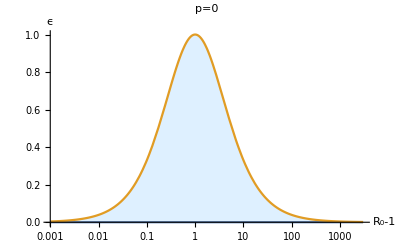

```mathematica
LogLinearPlot[{m[R],n[R]},{R,0.001,3000},PlotRange->{{0,3000},{0,1}},Filling->{1->{{2},{LightBlue,White}}},PlotLabel->"p=0",AxesLabel->{"R_0-1","ϵ"}]
```

```mathematica
Export["C:\\Users\\Roger Zhang\\Documents\\GitHub\\RogerZhang\\July_6th\\Figures\\p_0.pdf",%9,"PDF"]
```

C:\Users\Roger Zhang\Documents\GitHub\RogerZhang\July_6th\Figures\p_0.pdf